```mathematica
DSolve[y'[x]==Sin[5x],y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
DSolve[x^2y'[x]==y[x]-y[x]*x,y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
DSolve[{x^2Y'[x]==Y[x]-Y[x]*x,Y[1]==1/E},Y[x],x]
```

{{Y[x]→ⅇ^(-1/x)/x}}

```mathematica
DSolve[y''[x]+5y'[x]+2y[x]==0,y[x],x]
```

{{y[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
DSolve[{y''[x]+5y'[x]+2y[x]==0,y[0]==5,y'[0]==10},y[x],x]
```

{{y[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
NDSolve[{Y''[x]+x*Y[x]==0,Y[0]==1,Y[1]==1},Y[x],{x,-5,-10}]
```

{{Y[x]→InterpolatingFunction[{{-10.,-5.}},<>][x]}}

```mathematica
a=NDSolve[{Y''[x]+x*Y[x]==0,Y[0]==1,Y[1]==1},Y[x],{x,-5,10}]
```

{{Y[x]→InterpolatingFunction[{{-5.,10.}},<>][x]}}

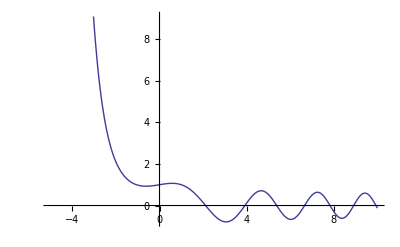

```mathematica
Plot[Evaluate[Y[x]/.a],{x,-5,10}]
```

```mathematica
Table[a,{x,-5,10,0.1}]
```

{{{Y[-5.]→406.12}},{{Y[-4.9]→326.867}},{{Y[-4.8]→263.707}},{{Y[-4.7]→213.266}},{{Y[-4.6]→172.895}},{{Y[-4.5]→140.513}},{{Y[-4.4]→114.484}},{{Y[-4.3]→93.5135}},{{Y[-4.2]→76.5821}},{{Y[-4.1]→62.8809}},{{Y[-4.]→51.7688}},{{Y[-3.9]→42.736}},{{Y[-3.8]→35.3766}},{{Y[-3.7]→29.367}},{{Y[-3.6]→24.4482}},{{Y[-3.5]→20.413}},{{Y[-3.4]→17.0948}},{{Y[-3.3]→14.3601}},{{Y[-3.2]→12.101}},{{Y[-3.1]→10.2304}},{{Y[-3.]→8.67815}},{{Y[-2.9]→7.3871}},{{Y[-2.8]→6.31099}},{{Y[-2.7]→5.41217}},{{Y[-2.6]→4.65994}},{{Y[-2.5]→4.02925}},{{Y[-2.4]→3.4996}},{{Y[-2.3]→3.05418}},{{Y[-2.2]→2.67921}},{{Y[-2.1]→2.36336}},{{Y[-2.]→2.09726}},{{Y[-1.9]→1.87323}},{{Y[-1.8]→1.68487}},{{Y[-1.7]→1.52692}},{{Y[-1.6]→1.39499}},{{Y[-1.5]→1.28543}},{{Y[-1.4]→1.19518}},{{Y[-1.3]→1.12171}},{{Y[-1.2]→1.06284}},{{Y[-1.1]→1.01675}},{{Y[-1.]→0.98186}},{{Y[-0.9]→0.956802}},{{Y[-0.8]→0.940365}},{{Y[-0.7]→0.931458}},{{Y[-0.6]→0.929076}},{{Y[-0.5]→0.932271}},{{Y[-0.4]→0.940128}},{{Y[-0.3]→0.951746}},{{Y[-0.2]→0.966217}},{{Y[-0.1]→0.982619}},{{Y[0.]→1.}},{{Y[0.1]→1.01738}},{{Y[0.2]→1.03374}},{{Y[0.3]→1.04803}},{{Y[0.4]→1.05917}},{{Y[0.5]→1.06607}},{{Y[0.6]→1.06765}},{{Y[0.7]→1.06283}},{{Y[0.8]→1.05057}},{{Y[0.9]→1.02991}},{{Y[1.]→1.}},{{Y[1.1]→0.960101}},{{Y[1.2]→0.909658}},{{Y[1.3]→0.848319}},{{Y[1.4]→0.775975}},{{Y[1.5]→0.692793}},{{Y[1.6]→0.599247}},{{Y[1.7]→0.496143}},{{Y[1.8]→0.384633}},{{Y[1.9]→0.26623}},{{Y[2.]→0.142797}},{{Y[2.1]→0.0165328}},{{Y[2.2]→-0.110056}},{{Y[2.3]→-0.234208}},{{Y[2.4]→-0.352963}},{{Y[2.5]→-0.463244}},{{Y[2.6]→-0.561951}},{{Y[2.7]→-0.646064}},{{Y[2.8]→-0.712759}},{{Y[2.9]→-0.759535}},{{Y[3.]→-0.784331}},{{Y[3.1]→-0.785653}},{{Y[3.2]→-0.762685}},{{Y[3.3]→-0.715382}},{{Y[3.4]→-0.644546}},{{Y[3.5]→-0.551872}},{{Y[3.6]→-0.439955}},{{Y[3.7]→-0.312267}},{{Y[3.8]→-0.173083}},{{Y[3.9]→-0.0273664}},{{Y[4.]→0.119389}},{{Y[4.1]→0.261361}},{{Y[4.2]→0.392631}},{{Y[4.3]→0.507448}},{{Y[4.4]→0.600505}},{{Y[4.5]→0.667223}},{{Y[4.6]→0.70402}},{{Y[4.7]→0.708552}},{{Y[4.8]→0.679915}},{{Y[4.9]→0.618779}},{{Y[5.]→0.52746}},{{Y[5.1]→0.409895}},{{Y[5.2]→0.271535}},{{Y[5.3]→0.119141}},{{Y[5.4]→-0.0395135}},{{Y[5.5]→-0.196018}},{{Y[5.6]→-0.341765}},{{Y[5.7]→-0.46844}},{{Y[5.8]→-0.568521}},{{Y[5.9]→-0.635773}},{{Y[6.]→-0.665691}},{{Y[6.1]→-0.655864}},{{Y[6.2]→-0.606238}},{{Y[6.3]→-0.519231}},{{Y[6.4]→-0.3997}},{{Y[6.5]→-0.254747}},{{Y[6.6]→-0.0933504}},{{Y[6.7]→0.074146}},{{Y[6.8]→0.236675}},{{Y[6.9]→0.383174}},{{Y[7.]→0.503365}},{{Y[7.1]→0.588507}},{{Y[7.2]→0.632101}},{{Y[7.3]→0.630453}},{{Y[7.4]→0.583066}},{{Y[7.5]→0.492808}},{{Y[7.6]→0.365838}},{{Y[7.7]→0.211264}},{{Y[7.8]→0.0405539}},{{Y[7.9]→-0.13327}},{{Y[8.]→-0.296607}},{{Y[8.1]→-0.436347}},{{Y[8.2]→-0.540961}},{{Y[8.3]→-0.601504}},{{Y[8.4]→-0.612461}},{{Y[8.5]→-0.572333}},{{Y[8.6]→-0.483911}},{{Y[8.7]→-0.354188}},{{Y[8.8]→-0.193898}},{{Y[8.9]→-0.0166977}},{{Y[9.]→0.161948}},{{Y[9.1]→0.326098}},{{Y[9.2]→0.460772}},{{Y[9.3]→0.553361}},{{Y[9.4]→0.594873}},{{Y[9.5]→0.580902}},{{Y[9.6]→0.512187}},{{Y[9.7]→0.39471}},{{Y[9.8]→0.239278}},{{Y[9.9]→0.060615}},{{Y[10.]→-0.123969}}}

```mathematica
b=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

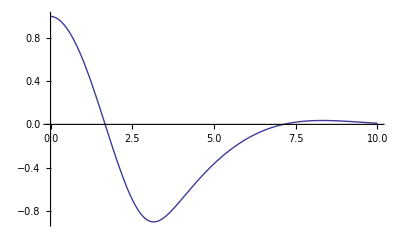

```mathematica
Plot[Evaluate[y[t]/.b],{t,0,10}]
```

```mathematica
Table[b,{t,0,10,1}]
```

{{{y[0]→1.}},{{y[1]→0.590672}},{{y[2]→-0.307456}},{{y[3]→-0.892432}},{{y[4]→-0.698048}},{{y[5]→-0.364728}},{{y[6]→-0.133941}},{{y[7]→-0.00917521}},{{y[8]→0.0339264}},{{y[9]→0.02942}},{{y[10]→0.0103315}}}

```mathematica
c=NDSolve[{y''[x]+0.3*y'[x]+Sin[y[x]]==0,y[0]==2,y'[0]==0},y[x],{x,0,30}]
```

{{y[x]→InterpolatingFunction[{{0.,30.}},<>][x]}}

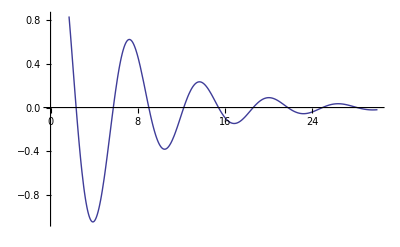

```mathematica
Plot[Evaluate[y[x]/.c],{x,0,30}]
```

```mathematica
Table[c,{x,0,30,1}]
```

{{{y[0]→2.}},{{y[1]→1.57619}},{{y[2]→0.449474}},{{y[3]→-0.69164}},{{y[4]→-1.04373}},{{y[5]→-0.593108}},{{y[6]→0.174734}},{{y[7]→0.60875}},{{y[8]→0.470861}},{{y[9]→0.00868367}},{{y[10]→-0.340276}},{{y[11]→-0.33317}},{{y[12]→-0.0675869}},{{y[13]→0.182451}},{{y[14]→0.223613}},{{y[15]→0.0776903}},{{y[16]→-0.0919303}},{{y[17]→-0.144709}},{{y[18]→-0.0691705}},{{y[19]→0.0416588}},{{y[20]→0.0906927}},{{y[21]→0.0550494}},{{y[22]→-0.0150582}},{{y[23]→-0.0550357}},{{y[24]→-0.0409491}},{{y[25]→0.00200693}},{{y[26]→0.0322352}},{{y[27]→0.0290249}},{{y[28]→0.00359218}},{{y[29]→-0.0181023}},{{y[30]→-0.0197942}}}